Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

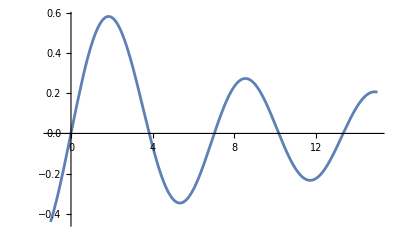

```mathematica
Plot[BesselJ[1,x], {x,-1,15}]
```

```mathematica
FindRoot[BesselJ[1,x]==0,{x,{0,4,7}}]
```

{x→{0.,3.83171,7.01559}}

Q5: Solve the following differential equation using both DSolve and NDSolve (for x=-10 to x=10). Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

```mathematica
real = DSolve[{y''[x]-x*y[x]==0,y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y[x],x]
```

{{y[x]→3^(2/3) AiryAi[x] Gamma[2/3]}}

```mathematica
numeric=NDSolve[{y''[x]-x*y[x]==0,y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y,{x,-10,10},Method->"ImplicitRungeKutta",AccuracyGoal->13,PrecisionGoal->13,MaxSteps->Infinity]
```

{{y→InterpolatingFunction[…]}}

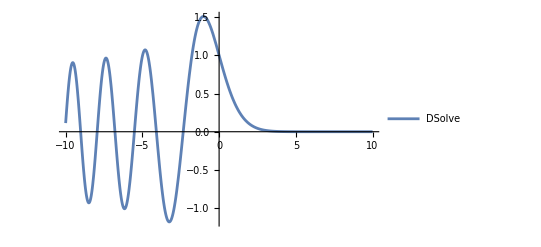

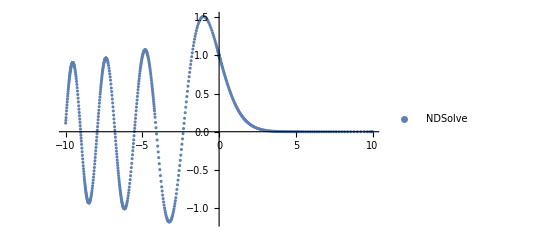

```mathematica
yreal=(y/.Flatten@real)[x];
ynum=(y/.Flatten@numeric)[x];
ynum[[0]]["ValuesOnGrid"];
Flatten@ynum[[0]]["Coordinates"];
ydat=Transpose[{%,%%}];
Plot[y[x]/. real,{x,-10,10},PlotLegends->{"DSolve"}]
ListPlot[ydat,PlotLegends->{"NDSolve"}]
```